## （前回の復習）

### (1) 平面内の直線を適当に定め，パラメーター表示し，ParametricPlot を用いて描画しなさい．

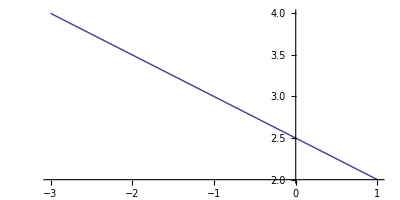

```mathematica
ParametricPlot[{2t-1,-t+3},{t,-1,1}]
```

### (2) 2次正方行列を適当に定め，それをAと定義しなさい．

```mathematica
A={{1,1},{-1,1/3}}
```

{{1,1},{-1,1/3}}

### (3) (1)の直線を(2)の行列Aで線形変換した直線を描画しなさい．

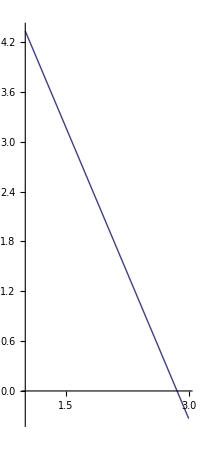

```mathematica
ParametricPlot[A.{2t-1,-t+3},{t,-1,1}]
```

### (4) (1)と(3)の直線ををひとつの座標平面に同時に描画しなさい．

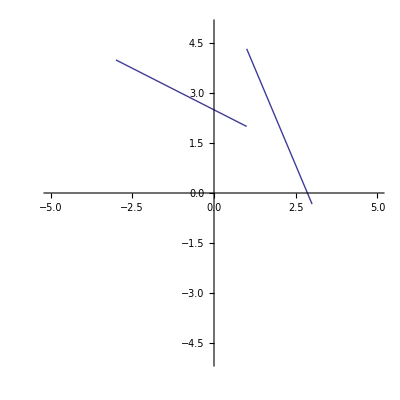

```mathematica
Show[
ParametricPlot[{2t-1,-t+3},{t,-1,1},PlotRange->{{-5,5},{-5,5}}],
ParametricPlot[A.{2t-1,-t+3},{t,-1,1}]
]
```

## 本日の演習

### Line コマンドで折れ線，または多角形を描画しよう．

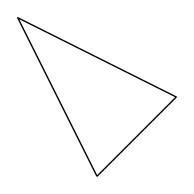

```mathematica
Graphics[Line[{{0,0},{1,1},{-1,2},{0,0}}]]
```

### 上の図形を行列Aで線形変換する．

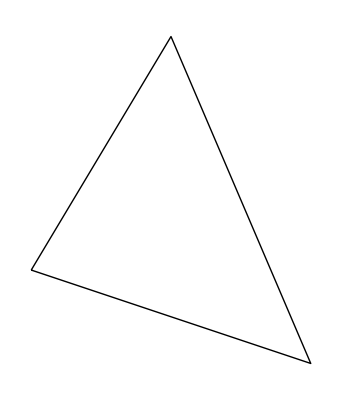

```mathematica
Graphics[Line[{A.{0,0},A.{1,1},A.{-1,2},A.{0,0}}]]
```

### 変換前と変換後の図形を同時に描画する．

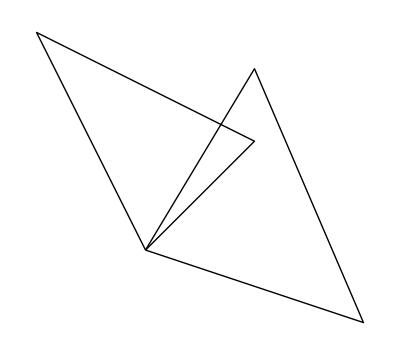

```mathematica
Show[
Graphics[Line[{{0,0},{1,1},{-1,2},{0,0}}]],
Graphics[Line[{A.{0,0},A.{1,1},A.{-1,2},A.{0,0}}]]
]
```

## 本日の課題１：次の各行列が定める線形変換によって図形を変換してみよ． （変換前と変換後の図形を同時に描画せよ）

### 相似変換

```mathematica
M1={{2,0},{0,2}}
```

{{2,0},{0,2}}

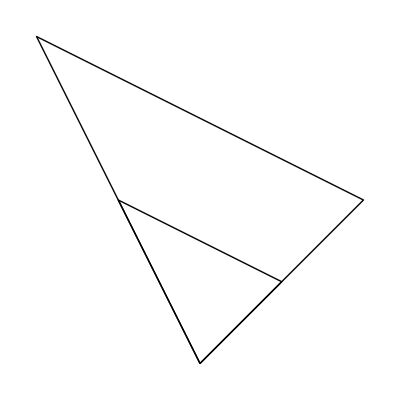

```mathematica
Show[
Graphics[Line[{{0,0},{1,1},{-1,2},{0,0}}]],
Graphics[Line[{M1.{0,0},M1.{1,1},M1.{-1,2},M1.{0,0}}]]
]
```

### せん断（横方向）

```mathematica
M2={{1,2},{0,1}}
```

{{1,2},{0,1}}

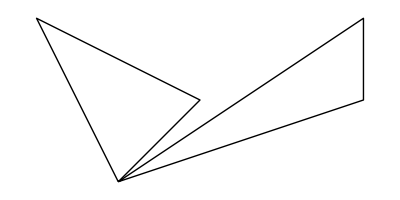

```mathematica
Show[
Graphics[Line[{{0,0},{1,1},{-1,2},{0,0}}]],
Graphics[Line[{M2.{0,0},M2.{1,1},M2.{-1,2},M2.{0,0}}]]
]
```

### せん断（縦方向）

```mathematica
M3={{1,0},{-1/2,1}}
```

{{1,0},{-1/2,1}}

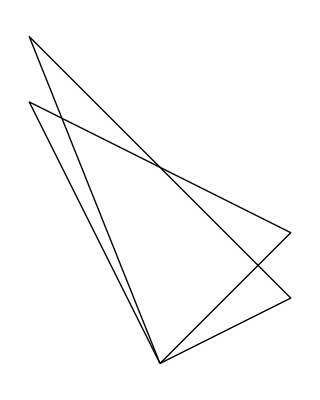

```mathematica
Show[
Graphics[Line[{{0,0},{1,1},{-1,2},{0,0}}]],
Graphics[Line[{M3.{0,0},M3.{1,1},M3.{-1,2},M3.{0,0}}]]
]
```

## 本日の課題２：課題１の各行列を変数つき行列として定義し，変換のアニメーションをつくりなさい．

### 相似変換

```mathematica
H2[x_]:={{x,0},{0,x}};
```

```mathematica
Manipulate[
Show[
Graphics[Line[{{0,0},{1,1},{-1,2},{0,0}}]],
Graphics[Line[{H2[x].{0,0},H2[x].{1,1},H2[x].{-1,2},H2[x].{0,0}}]]
],{x,-2,2},SaveDefinitions->True]
```

一方に色をつけてみます（変換後を赤で描画）．さらに，スケールを固定します．

```mathematica
Manipulate[
Show[
Graphics[Line[{{0,0},{1,1},{-1,2},{0,0}}],PlotRange->{{-5,5},{-5,5}}],
Graphics[{Red,Line[{H2[x].{0,0},H2[x].{1,1},H2[x].{-1,2},H2[x].{0,0}}]}]
],{{x,1,x},-2,2},SaveDefinitions->True]
```

### せん断（横方向）

```mathematica
Sx2[x_]:={{1,x},{0,1}};
```

```mathematica
Manipulate[Show[
Graphics[Line[{{0,0},{1,1},{-1,2},{0,0}}],PlotRange->{{-5,5},{-1,5}}],
Graphics[{Red,Line[{Sx2[x].{0,0},Sx2[x].{1,1},Sx2[x].{-1,2},Sx2[x].{0,0}}]}]
],{{x,0,x},-2,2},SaveDefinitions->True]
```

### せん断（縦方向）

```mathematica
Sy2[x_]:={{1,0},{x,1}};
```

```mathematica
Manipulate[Show[
Graphics[Line[{{0,0},{1,1},{-1,2},{0,0}}],PlotRange->{{-5,5},{-1,5}}],
Graphics[{Red,Line[{Sy2[x].{0,0},Sy2[x].{1,1},Sy2[x].{-1,2},Sy2[x].{0,0}}]}]
],{{x,0,x},-2,2},SaveDefinitions->True]
```